# Agent Network

## Create Base/Seed Network

```mathematica
network[nodes_,conn_]:=Flatten[Table[Table[i->Mod[i+j,nodes,1],{i,1,If[j≥Quotient[nodes+1,2],nodes/2,nodes],1}],{j,1,conn-1,1}]]
```

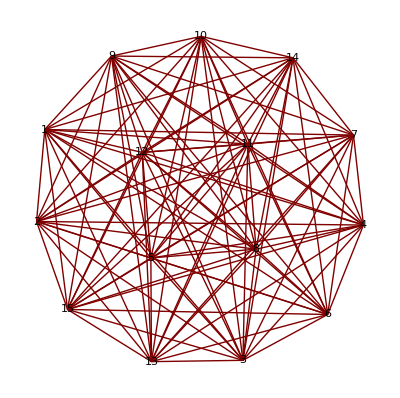

```mathematica
g = GraphPlot[network[15,8],DirectedEdges->False, VertexLabeling->True]
```